```mathematica
InverseNull[n_]:=First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==n&]]
```

```mathematica
Select[Table[Simplify[ allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0]],{k,Keys[allGraphs]}],Length[ListofVars[#]]==2&]:
```

{n1x2x3>n12x3,n1x23>n123,n13x2>n123,n12x3>n123,n1x2x3>n13x2,n1x2x3>n1x23}

```mathematica
lattice=Map[InverseNull[#[[1]]]->InverseNull[#[[2]]]&, Select[Table[Simplify[ allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0]],{k,Keys[allGraphs]}],Length[ListofVars[#]]==2&]]
```

{0→18,2→26,6→26,18→26,0→6,0→2}

```mathematica
direct=Table[
Table[
{
If[ToString[allGraphs[c[[1]],"comp"]]=="Greater",
 k->c[[2]]
];
If[ToString[allGraphs[c[[2]],"comp"]]=="Greater",
k->c[[1]]
]
}
,{c,allGraphs[k,"children"]}
]
,
{k,Keys[allGraphs]}
]//Flatten//DeleteDuplicates
```

{0→9,0→3,0→1,9→12,9→10,12→13,10→13,18→22,3→12,3→4,4→13,6→16,1→10,1→4,2→14}

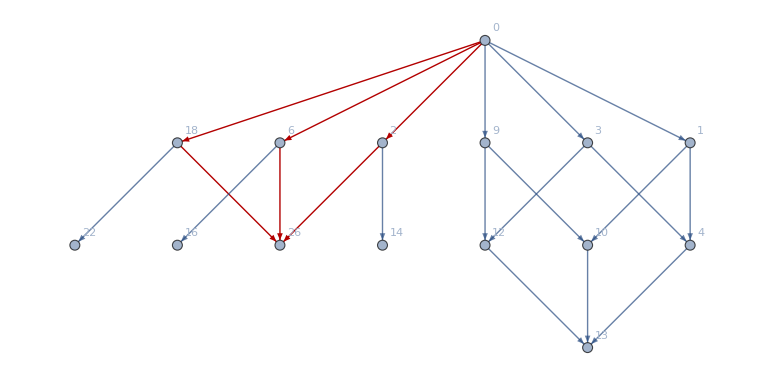

```mathematica
Graph[DeleteDuplicates[Join[lattice,direct]], VertexLabels->Table[k->Labeled[allGraphs[k,"graph"],Style[k,Blue, Bold]],{k,Keys[allGraphs]}],GraphHighlight->lattice,
GraphLayout->"LayeredDigraphEmbedding"]
```